```mathematica
(* Parameters that go into the model *)
(* Those that rely on mass have been made into functions for better exploration *)
ClearAll["Global`*"];
s=1;
B0=4.7*10^(-2);
Em=5774(*J/gram*);
η=3/4;
γ=1.19;
ζ=1.00;
fatscale[M_]:=M^(1-η);
f0[M_]:=fatscale[M]*0.0202;
musclescale[M_]:=M^(1-ζ);
mm0[M_]:=musclescale[M]*0.383;
α=(*2.10*10^(-9)*)(9.45*10^(-9));
Ed=18200; (*J/g*)
k=(*5*)23000;
(*k=(*10*)23000/2;*)
ρ[M_]:=B0*M^(η)/(M*Ed);
Y[M_]:=M*Ed/BLam[M]; (*g individual/ g grass*)

a0 = 1.88*10^-8 ;(*sec grams^-b0*)
a1=1.45*10^-7;
a2=4.04*10^6;
b0=-0.56;
b1=-0.27;
b2=0.30;
μ[M_] := (a0*(Exp[a1*a2*M^(b1+b2)]-1)*M^(b0-b1-b2))/(a1*a2)   (* this is the consumer death rate*)


B0=4.7*10^(-2);(*W g^−0.75*)
Em=5774;(*J/gram*)
a = B0/Em;
m0[M_]:= (.0558*(1/1000)^.92*M^0.92)*1000;
ϵLam = 0.95;
τLam[M_]:= -Log[(1-ϵLam^(1/4))/(1 - (m0[M]/M)^(1/4))]*(4*M^(1/4))/a;
λ[M_]:=(Log[2]/τLam[M]) (*Fecundity = 2*) (* max consumer growth rate *)




E'=7000; (*J/g*)
a'=B0/E';
m[t_,M_]:=M*E^(-a'*t/(M^(1-η)))


(* Two version of Beta-lambda here. The first one doesn't take long to integrate numerically but gives slightly different results from the analytical version below *)
Bλ[M_]=Integrate[B0*m[t,M]^(η),{t,0,τLam[M]}];

BLam[M_]:=1/(3 a)ⅇ^(-(a τLam[M])/M^(1/4)) M^(1/4) (3 (-1+ⅇ^((a τLam[M])/M^(1/4))) m0[M]+M (-48 ⅇ^((3 a τLam[M])/(4 M^(1/4))) (-1+(m0[M]/M)^(1/4))-36 ⅇ^((a τLam[M])/(2 M^(1/4))) (-1+(m0[M]/M)^(1/4))^2-16 ⅇ^((a τLam[M])/(4 M^(1/4))) (-1+(m0[M]/M)^(1/4))^3+3 (-1+4 (m0[M]/M)^(1/4)-6 √(m0[M]/M)+4 (m0[M]/M)^(3/4))+ⅇ^((a τLam[M])/M^(1/4)) (-25+12 (m0[M]/M)^(1/4)+6 √(m0[M]/M)+4 (m0[M]/M)^(3/4)))+3 a ⅇ^((a τLam[M])/M^(1/4)) M^(3/4) τLam[M]);
```

```mathematica
(* This is per-capita consumer growth *)
(* For a given value of M, lambda and mu will be constants and the percapita growth of the consumer will be a function of resource density *)
(* λ * R/k - μ *)
(* R here is resource density*)
Manipulate[
LogLogPlot[
{(λ[M]*R)/k-μ[M]},
{M,1,10^8},
Frame->True,FrameLabel->{"Mass (grams)","per capita consumer growth rate "},PlotLegends->{"growth rate"}],
{{R,100},0,50000}]
```

```mathematica
(* per capita resource and consumer growth rates for different population values *)
(* R here is resource density, P is consumer density *)
Manipulate[
LogLogPlot[
{α *(1-R/k)-((λ[M]/Y[M])/k+ρ[M]/R)* P,
{(λ[M]*R)/k-μ[M]}},
{M,1,10^8},
Frame->True,FrameLabel->{"Mass (grams)","per capita resource growth rate"},PlotLegends->{"resource growth", "consumer growth"}],
{{R,100},0,50000},{{P,5},0,1000}]
```

```mathematica
(* For a given value of M, lambdam, Y, and rho (maintenance) will be a function of resource and consumer density *)
(* α *(1-R/k)-((λ/Y)/k+ρ/R)* P *)
(* R here is resource density, P is consumer density *)
Manipulate[
LogPlot[
{α *(1-R/k)-((λ[M]/Y[M])/k+ρ[M]/R)* P},
{M,1,10^8},
Frame->True,FrameLabel->{"Mass (grams)","per capita resource growth rate"},PlotLegends->{"growth rate"}],
{{R,100},0,50000},{{P,5},0,1000}]
```

```mathematica
tmax=6*10^8;
(* This is the basic formulation of the 1 resource, consumer-resource model where full and hungry are combined *)
(* All parameters are either fixed physiological values, functions of mass, or are carrying capacity k (=23000 ) *)
Manipulate[lv=
NDSolve[
{P'[t]==(λ[M]/k) R[t]*P[t]-μ[M] P[t],
 R'[t]==α R[t](1-R[t]/k)-((λ[M]/Y[M])(R[t]/k)+ρ[M]) P[t],
P[0]==P0,R[0]==R0},
{P[t],R[t]},{t,0,tmax}];
Plot[Evaluate[{P[t],R[t]}/.lv],{t,0,tmax},PlotRange->All,AxesOrigin->{0,0},Frame->True,FrameLabel->{"Time (s)","Population Dynamics"},PlotLegends->{"Consumer", "Resource"}],
{{lv,{}},None},{{P0,1},0,1000,1},{{R0,23000},0,30000,1},{{M,1000},1,10000,5}];
```

```mathematica
{{P->0,R->0},{P->0,R->k},

{P->(k Y α (λ-μ) μ)/(λ^2 (μ+Y ρ)),
R->(k μ)/λ}}
```

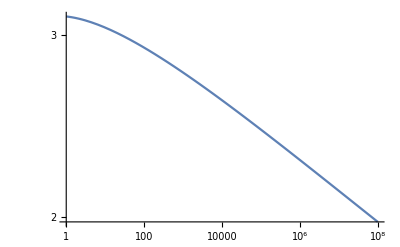

```mathematica
(* equlibrium density of consumers*)
LogLogPlot[(k*Y[M]*α*(λ[M]-μ[M])*μ[M])/(λ[M]^2 (μ[M]+Y[M]* ρ[M])),{M,1,1*10^8}]
```

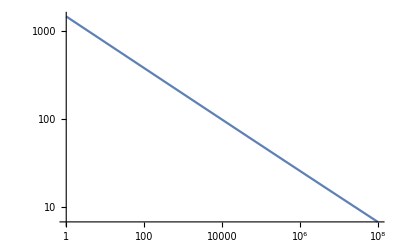

```mathematica
(* equilibrium density of resource *)
LogLogPlot[(k μ[M])/λ[M],{M,1,1*10^8}]
```

```mathematica
Con[M]:=(k μ[M])/λ[M];
```

```mathematica
tmax=10000000000;
(* This is the basic formulation of the 1 resource, consumer-resource model where full and hungry are combined *)
(* All parameters are either fixed physiological values, functions of mass, or are carrying capacity k (=23000 ) *)
Manipulate[lv=
NDSolve[
{P'[t]==(λ[M]/k) R[t]*P[t]-μ[M] P[t],
 R'[t]==α R[t](1-R[t]/k)-((λ[M]/Y[M])*(R[t]/k)+ρ[M]) P[t],
P[0]==P0,R[0]==R0},
{P[t],R[t]},{t,0,tmax},MaxSteps->Infinity,InterpolationOrder->All];
Plot[Evaluate[{P[t],R[t]}/.lv],{t,0,tmax},PlotRange->All,AxesOrigin->{0,0},Frame->True,FrameLabel->{"Time (s)","Population Dynamics"},PlotLegends->{"Consumer", "Resource"}],
{{lv,{}},None},{{P0,equil[M]},0,1000,1},{{R0,23000},0,30000,1},{{M,100000},1,1*10^8,5}];
```

```mathematica
Solve[{0==λ/k*R*P-μ*P,
0==α*R*(1-R/k)-((λ/Y)*(R/k)+ρ)*P},{P,R}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{P→0.,R→0.},{P→0.,R→23000.},{P→(0.00021735 (Y λ μ-1. Y μ^2))/(λ^2 (μ+Y ρ)),R→(23000. μ)/λ}}

```mathematica
M=100000;
parameters[M_]={
(*lambda*) λ[M],
(*mu*)μ[M],
(*Y*)Y[M],
(*rho*)ρ[M]
};

ξ=50;
params=parameters[M];

pEquil[M_]:=(k*Y[M]*α*(λ[M]-ξ*μ[M])*ξ*μ[M])/(λ[M]^2*(ξ*μ[M]+Y[M]*ρ[M]));
rEquil[M_]:=k*ξ*μ[M]/λ[M];

pE=pEquil[M];
rE=rEquil[M];

sol=NDSolve[
{P'[t]==(params[[1]]/k) R[t]*P[t]-dial*params[[2]]* P[t],
 R'[t]==α R[t](1-R[t]/k)-((params[[1]]/params[[3]])*(R[t]/k)+params[[4]]) P[t],
P[0]==pE,R[0]==rE},
{P[t],R[t]},{t,0,tmax},MaxSteps->Infinity,InterpolationOrder->All];

(*LogLogPlot[Evaluate[{P[t],R[t]}/.sol],{t,0,tmax},PlotRange->All,AxesOrigin->{0,0},Frame->True,FrameLabel->{"Time (s)","Population Dynamics"},PlotLegends->{"Consumer", "Resource"}]*)
```

NDSolve::ndnl: Endpoint tmax in {t,0.,tmax} is not a real number.

```mathematica
pE
```

2.43085

```mathematica
(* checking whether parameters are the same in mine*)
```

```mathematica
M=100000;
λ[M] (* 2.0999659778308515*^-8 *)
μ[M] (* 5.998862115609031*^-7 *)   (* this is the starving mortality rate not the appendix death term*)
Y[M] (* 0.0008959637089986015*)
ρ[M]  (* 1.7829563434634398*^-8 *)
```

2.09997×10^-8

4.63617×10^-11

0.000895964

1.4522×10^-7

```mathematica
(λ[M]/k) R[t]*P[t]-μ[M] P[t],
 R'[t]==α R[t](1-R[t]/k)-((λ[M]/Y[M])*(R[t]/k)+ρ[M]
```